```mathematica
acastraj= Piecewise[{{c*x^2, x<b}, {b*c*(2x-b), True}}]
```

Piecewise[{{c x^2, x<b}, {b c (-b+2 x), True}}]

```mathematica
Piecewise[{{c x^2, x<b}, {b c (-b+2 x), True}}]
```

Piecewise[{{c x^2, x<b}, {b c (-b+2 x), True}}]

```mathematica
D[acastraj, x]
```

```mathematica
Piecewise[{{2 c x, b-x>0}, {2 b c, True}}]
```

Piecewise[{{2 c x, b-x>0}, {2 b c, True}}]

```mathematica
Simplify[Piecewise[{{2 c x,b-x>0}},2 b c]]
```

Piecewise[{{2 c x, b>x}, {2 b c, True}}]

```mathematica
MaxMemoryUsed[rectcond = Resolve[ForAll[x, !RegionMember[Rectangle[{x-w, acastraj-h}, {x+w, acastraj+h}], {xo, yo}]], Reals]]
```

1436584

```mathematica
Timing[rectcond = Resolve[ForAll[x, !RegionMember[Rectangle[{x-w, acastraj-h}, {x+w, acastraj+h}], {xo, yo}]], Reals]]
```

{0.107945,(w<0||b+w-xo≤0||-h+c w^2-2 c w xo+c xo^2-yo>0||h+c w^2-2 c w xo+c xo^2-yo<0)&&(w<0||b-w-xo≤0||-h+c w^2+2 c w xo+c xo^2-yo>0||h+c w^2+2 c w xo+c xo^2-yo<0)&&(w<0||b+w-xo>0||b^2 c-h+2 b c w-2 b c xo+yo>0||b^2 c+h+2 b c w-2 b c xo+yo<0)&&(w<0||b-w-xo>0||b^2 c-h-2 b c w-2 b c xo+yo>0||b^2 c+h-2 b c w-2 b c xo+yo<0)&&(b-w-xo>0||b+w-xo<0||b^2 c-h-yo>0||b^2 c+h-yo<0)&&(b==0||c==0||h<0||b^3 c^2-b c h-b c yo>0||b^3 c^2+b c h-2 b^2 c^2 w-2 b^2 c^2 xo+b c yo>0||b^3 c^2+b c h+2 b^2 c^2 w-2 b^2 c^2 xo+b c yo<0)&&(b==0||c==0||h<0||b^3 c^2+b c h-b c yo>0||b^3 c^2-b c h-2 b^2 c^2 w-2 b^2 c^2 xo+b c yo>0||b^3 c^2-b c h+2 b^2 c^2 w-2 b^2 c^2 xo+b c yo<0)&&(b≤0||c==0||h<0||w-xo<0||c h-c yo>0||c h+c^2 w^2-2 c^2 w xo+c^2 xo^2-c yo<0||c h+c^2 w^2+2 c^2 w xo+c^2 xo^2-c yo>0)&&(c==0||h<0||w-xo<0||c h-c yo>0||b^2 c^2+c h-c yo≥0||c h+c^2 w^2-2 c^2 w xo+c^2 xo^2-c yo<0||c h+c^2 w^2+2 c^2 w xo+c^2 xo^2-c yo>0)&&(b≤0||c==0||h<0||w-xo<0||-c h+c^2 w^2-2 c^2 w xo+c^2 xo^2-c yo<0||-c h+c^2 w^2+2 c^2 w xo+c^2 xo^2-c yo>0||c h+c yo<0)&&(c==0||h<0||w-xo<0||b^2 c^2-c h-c yo≥0||-c h+c^2 w^2-2 c^2 w xo+c^2 xo^2-c yo<0||-c h+c^2 w^2+2 c^2 w xo+c^2 xo^2-c yo>0||c h+c yo<0)&&(b≤0||c==0||h≠0||w-xo<0||c h-c yo>0||c h+c^2 w^2-2 c^2 w xo+c^2 xo^2-c yo<0||c h+c^2 w^2+2 c^2 w xo+c^2 xo^2-c yo>0)&&(c==0||h≠0||w-xo<0||c h-c yo>0||b^2 c^2+c h-c yo≥0||c h+c^2 w^2-2 c^2 w xo+c^2 xo^2-c yo<0||c h+c^2 w^2+2 c^2 w xo+c^2 xo^2-c yo>0)&&(b≤0||c==0||h≠0||w-xo<0||-c h+c^2 w^2-2 c^2 w xo+c^2 xo^2-c yo<0||-c h+c^2 w^2+2 c^2 w xo+c^2 xo^2-c yo>0||c h+c yo<0)&&(c==0||h≠0||w-xo<0||b^2 c^2-c h-c yo≥0||-c h+c^2 w^2-2 c^2 w xo+c^2 xo^2-c yo<0||-c h+c^2 w^2+2 c^2 w xo+c^2 xo^2-c yo>0||c h+c yo<0)&&(b≤0||c==0||h<0||w-xo<0||w+xo<0||c h-c yo>0||c h+c^2 w^2-2 c^2 w xo+c^2 xo^2-c yo<0||c h+c^2 w^2+2 c^2 w xo+c^2 xo^2-c yo<0)&&(b≤0||c==0||h<0||w-xo<0||w+xo<0||-c h+c^2 w^2-2 c^2 w xo+c^2 xo^2-c yo<0||-c h+c^2 w^2+2 c^2 w xo+c^2 xo^2-c yo<0||c h+c yo<0)&&(b≤0||c==0||h<0||w+xo<0||c h-c yo>0||b^2 c^2+c h-c yo≤0||c h+c^2 w^2-2 c^2 w xo+c^2 xo^2-c yo>0||c h+c^2 w^2+2 c^2 w xo+c^2 xo^2-c yo<0)&&(b≤0||c==0||h<0||w+xo<0||b^2 c^2-c h-c yo≤0||-c h+c^2 w^2-2 c^2 w xo+c^2 xo^2-c yo>0||-c h+c^2 w^2+2 c^2 w xo+c^2 xo^2-c yo<0||c h+c yo<0)&&(b≤0||c==0||h≠0||w-xo<0||w+xo<0||c h-c yo>0||c h+c^2 w^2-2 c^2 w xo+c^2 xo^2-c yo<0||c h+c^2 w^2+2 c^2 w xo+c^2 xo^2-c yo<0)&&(b≤0||c==0||h≠0||w-xo<0||w+xo<0||-c h+c^2 w^2-2 c^2 w xo+c^2 xo^2-c yo<0||-c h+c^2 w^2+2 c^2 w xo+c^2 xo^2-c yo<0||c h+c yo<0)&&(b≤0||c==0||h≠0||w+xo<0||c h-c yo>0||b^2 c^2+c h-c yo≤0||c h+c^2 w^2-2 c^2 w xo+c^2 xo^2-c yo>0||c h+c^2 w^2+2 c^2 w xo+c^2 xo^2-c yo<0)&&(b≤0||c==0||h≠0||w+xo<0||b^2 c^2-c h-c yo≤0||-c h+c^2 w^2-2 c^2 w xo+c^2 xo^2-c yo>0||-c h+c^2 w^2+2 c^2 w xo+c^2 xo^2-c yo<0||c h+c yo<0)&&(c≤0||h<0||w-xo<0||w+xo<0||b^2 c+h-yo≥0||h+c w^2-2 c w xo+c xo^2-yo<0||h+c w^2+2 c w xo+c xo^2-yo<0||yo≤0)&&(c≥0||h<0||w-xo<0||w+xo<0||b^2 c+h-yo≤0||h+c w^2-2 c w xo+c xo^2-yo>0||h+c w^2+2 c w xo+c xo^2-yo>0)&&(c≤0||h<0||w-xo<0||w+xo<0||b^2 c-h-yo≥0||-h+c w^2-2 c w xo+c xo^2-yo<0||-h+c w^2+2 c w xo+c xo^2-yo<0)&&(c≥0||h<0||w-xo<0||w+xo<0||b^2 c-h-yo≤0||-h+c w^2-2 c w xo+c xo^2-yo>0||-h+c w^2+2 c w xo+c xo^2-yo>0||yo≥0)&&(c≤0||h≠0||w-xo<0||w+xo<0||b^2 c+h-yo≥0||h+c w^2-2 c w xo+c xo^2-yo<0||h+c w^2+2 c w xo+c xo^2-yo<0||yo≤0)&&(c≥0||h≠0||w-xo<0||w+xo<0||b^2 c+h-yo≤0||h+c w^2-2 c w xo+c xo^2-yo>0||h+c w^2+2 c w xo+c xo^2-yo>0||yo≥0)&&(c≤0||h≠0||w-xo<0||w+xo<0||b^2 c-h-yo≥0||-h+c w^2-2 c w xo+c xo^2-yo<0||-h+c w^2+2 c w xo+c xo^2-yo<0||yo≤0)&&(c≥0||h≠0||w-xo<0||w+xo<0||b^2 c-h-yo≤0||-h+c w^2-2 c w xo+c xo^2-yo>0||-h+c w^2+2 c w xo+c xo^2-yo>0||yo≥0)}

```mathematica
rectcond/.w-> 2 /. h-> 1 /. b-> 4 /. c-> 0.25
```

(6-xo≤0||0.-1. xo+0.25 xo^2-yo>0||2.-1. xo+0.25 xo^2-yo<0)&&(2-xo≤0||0.+1. xo+0.25 xo^2-yo>0||2.+1. xo+0.25 xo^2-yo<0)&&(6-xo>0||7.-2. xo+yo>0||9.-2. xo+yo<0)&&(2-xo>0||-1-2. xo+yo>0||1-2. xo+yo<0)&&(2-xo>0||6-xo<0||3.-yo>0||5.-yo<0)&&(3.-1. yo>0||1.-2. xo+1. yo>0||9.-2. xo+1. yo<0)&&(5.-1. yo>0||-1.-2. xo+1. yo>0||7.-2. xo+1. yo<0)&&(2-xo<0||0.25-0.25 yo>0||0.5-0.25 xo+0.0625 xo^2-0.25 yo<0||0.5+0.25 xo+0.0625 xo^2-0.25 yo>0)&&(2-xo<0||0.25-0.25 yo>0||1.25-0.25 yo≥0||0.5-0.25 xo+0.0625 xo^2-0.25 yo<0||0.5+0.25 xo+0.0625 xo^2-0.25 yo>0)&&(2-xo<0||0.-0.25 xo+0.0625 xo^2-0.25 yo<0||0.+0.25 xo+0.0625 xo^2-0.25 yo>0||0.25+0.25 yo<0)&&(2-xo<0||0.75-0.25 yo≥0||0.-0.25 xo+0.0625 xo^2-0.25 yo<0||0.+0.25 xo+0.0625 xo^2-0.25 yo>0||0.25+0.25 yo<0)&&(2-xo<0||2+xo<0||0.25-0.25 yo>0||0.5-0.25 xo+0.0625 xo^2-0.25 yo<0||0.5+0.25 xo+0.0625 xo^2-0.25 yo<0)&&(2-xo<0||2+xo<0||0.-0.25 xo+0.0625 xo^2-0.25 yo<0||0.+0.25 xo+0.0625 xo^2-0.25 yo<0||0.25+0.25 yo<0)&&(2+xo<0||0.25-0.25 yo>0||1.25-0.25 yo≤0||0.5-0.25 xo+0.0625 xo^2-0.25 yo>0||0.5+0.25 xo+0.0625 xo^2-0.25 yo<0)&&(2+xo<0||0.75-0.25 yo≤0||0.-0.25 xo+0.0625 xo^2-0.25 yo>0||0.+0.25 xo+0.0625 xo^2-0.25 yo<0||0.25+0.25 yo<0)&&(2-xo<0||2+xo<0||5.-yo≥0||2.-1. xo+0.25 xo^2-yo<0||2.+1. xo+0.25 xo^2-yo<0||yo≤0)&&(2-xo<0||2+xo<0||3.-yo≥0||0.-1. xo+0.25 xo^2-yo<0||0.+1. xo+0.25 xo^2-yo<0)

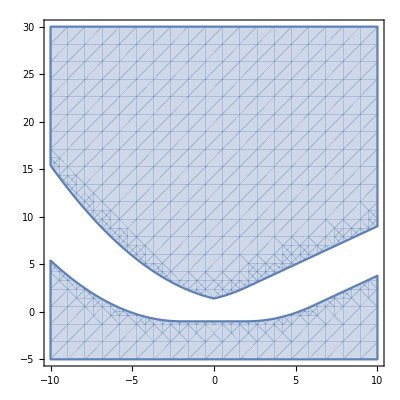

```mathematica
RegionPlot[rectcond/.w-> 2 /. h-> 1 /. b-> 4 /. c-> 0.1, {xo, -10, 10}, {yo, -5, 30}]
```

```mathematica
MaxMemoryUsed[rectcond = Resolve[ForAll[x, Abs[x - xo] >w || Abs[acastraj- yo] > h], Reals]]
```

1823024

```mathematica
Timing[rectcond = Resolve[ForAll[x, Abs[x - xo] >w || Abs[acastraj- yo] > h], Reals]]
```

{1.10105,1}
 |  |  |  |

```mathematica
RegionPlot[rectcond/.w-> 2 /. h-> 1 /. b-> 4 /. c-> 0.1, {xo, -10, 10}, {yo, -5, 30}]
```

-Graphics-

```mathematica
MaxMemoryUsed[rectcond = Resolve[ForAll[x, !RegionMember[Rectangle[{x-2, acastraj-1}, {x+2, acastraj+1}], {xo, yo}]], Reals]]
```

324752

```mathematica
Timing[rectcond = Resolve[ForAll[x, !RegionMember[Rectangle[{x-2, acastraj-1}, {x+2, acastraj+1}], {xo, yo}]], Reals]]
```

{0.198213,(b-xo≤-2||4 c-4 c xo+c xo^2-yo>1||4 c-4 c xo+c xo^2-yo<-1)&&(b-xo≤2||4 c+4 c xo+c xo^2-yo>1||4 c+4 c xo+c xo^2-yo<-1)&&(b-xo>-2||4 b c+b^2 c-2 b c xo+yo>1||4 b c+b^2 c-2 b c xo+yo<-1)&&(b-xo>2||-4 b c+b^2 c-2 b c xo+yo>1||-4 b c+b^2 c-2 b c xo+yo<-1)&&(b-xo>2||b-xo<-2||b^2 c-yo>1||b^2 c-yo<-1)&&(b==0||c==0||-b c+b^3 c^2-b c yo>0||b c-4 b^2 c^2+b^3 c^2-2 b^2 c^2 xo+b c yo>0||b c+4 b^2 c^2+b^3 c^2-2 b^2 c^2 xo+b c yo<0)&&(b==0||c==0||b c+b^3 c^2-b c yo>0||-b c-4 b^2 c^2+b^3 c^2-2 b^2 c^2 xo+b c yo>0||-b c+4 b^2 c^2+b^3 c^2-2 b^2 c^2 xo+b c yo<0)&&(b≤0||c==0||xo>2||c+4 c^2-4 c^2 xo+c^2 xo^2-c yo<0||c+4 c^2+4 c^2 xo+c^2 xo^2-c yo>0||-c+c yo<0)&&(c==0||xo>2||c+b^2 c^2-c yo≥0||c+4 c^2-4 c^2 xo+c^2 xo^2-c yo<0||c+4 c^2+4 c^2 xo+c^2 xo^2-c yo>0||-c+c yo<0)&&(b≤0||c==0||xo>2||-c+4 c^2-4 c^2 xo+c^2 xo^2-c yo<0||-c+4 c^2+4 c^2 xo+c^2 xo^2-c yo>0||c+c yo<0)&&(c==0||xo>2||-c+b^2 c^2-c yo≥0||-c+4 c^2-4 c^2 xo+c^2 xo^2-c yo<0||-c+4 c^2+4 c^2 xo+c^2 xo^2-c yo>0||c+c yo<0)&&(b≤0||c==0||xo>2||xo<-2||c+4 c^2-4 c^2 xo+c^2 xo^2-c yo<0||c+4 c^2+4 c^2 xo+c^2 xo^2-c yo<0||-c+c yo<0)&&(b≤0||c==0||xo<-2||c+b^2 c^2-c yo≤0||c+4 c^2-4 c^2 xo+c^2 xo^2-c yo>0||c+4 c^2+4 c^2 xo+c^2 xo^2-c yo<0||-c+c yo<0)&&(b≤0||c==0||xo>2||xo<-2||-c+4 c^2-4 c^2 xo+c^2 xo^2-c yo<0||-c+4 c^2+4 c^2 xo+c^2 xo^2-c yo<0||c+c yo<0)&&(b≤0||c==0||xo<-2||-c+b^2 c^2-c yo≤0||-c+4 c^2-4 c^2 xo+c^2 xo^2-c yo>0||-c+4 c^2+4 c^2 xo+c^2 xo^2-c yo<0||c+c yo<0)&&(c≤0||xo>2||xo<-2||b^2 c-yo≥-1||4 c-4 c xo+c xo^2-yo<-1||4 c+4 c xo+c xo^2-yo<-1||yo≤1)&&(c≥0||xo>2||xo<-2||b^2 c-yo≤-1||4 c-4 c xo+c xo^2-yo>-1||4 c+4 c xo+c xo^2-yo>-1||yo≥1)&&(c≤0||xo>2||xo<-2||b^2 c-yo≥1||4 c-4 c xo+c xo^2-yo<1||4 c+4 c xo+c xo^2-yo<1||yo≤-1)&&(c≥0||xo>2||xo<-2||b^2 c-yo≤1||4 c-4 c xo+c xo^2-yo>1||4 c+4 c xo+c xo^2-yo>1||yo≥-1)}

```mathematica
Timing[rectcond=Resolve[ForAll[x, !RegionMember[Rectangle[{x-w, (acastraj/.b -> 2 /. c-> 0.25)-h}, {x+w, (acastraj/.b -> 2 /. c-> 0.25)+h}], {xo, yo}]], Reals]]
```

{0.043827,(w<0||w-xo≤-2||4. h+1. w^2-2. w xo+1. xo^2-4. yo<0||4. h-1. w^2+2. w xo-1. xo^2+4. yo<0)&&(w<0||w+xo<2||1. h+1. w+1. xo-1. yo<1.||1. h-1. w-1. xo+1. yo<-1.)&&(w<0||w-xo>-2||xo≤0||1. h-1. w+1. xo-1. yo<1.||1. h+1. w-1. xo+1. yo<-1.)&&(w<0||w+xo≥2||4. h+1. w^2+2. w xo+1. xo^2-4. yo<0||4. h-1. w^2-2. w xo-1. xo^2+4. yo<0)&&(w-xo<-2||w+xo<2||1. h-1. yo<-1.||1. h+1. yo<1.)&&(h<0||1. h+1. w+1. xo-1. yo<1.||yo≤0||-1. h+1. yo<1.||-1. h+1. w-1. xo+1. yo<-1.)&&(h<0||-1. h+1. w+1. xo-1. yo<1.||1. h+1. yo<1.||1. h+1. w-1. xo+1. yo<-1.)&&(h≠0||1. w-1. xo<0||4. h+1. w^2-2. w xo+1. xo^2-4. yo<0||yo<0||-4. h-1. w^2-2. w xo-1. xo^2+4. yo<0)&&(h≠0||1. w-1. xo<0||-4. h+1. w^2-2. w xo+1. xo^2-4. yo<0||yo<0||4. h-1. w^2-2. w xo-1. xo^2+4. yo<0)&&(h<0||1. w-1. xo<0||4. h+1. w^2-2. w xo+1. xo^2-4. yo<0||yo<0||-1. h+1. yo<0||-4. h-1. w^2-2. w xo-1. xo^2+4. yo<0)&&(h≠0||1. w-1. xo<0||1. w+1. xo<0||4. h+1. w^2-2. w xo+1. xo^2-4. yo<0||4. h+1. w^2+2. w xo+1. xo^2-4. yo<0||yo<0)&&(h≠0||1. w-1. xo<0||1. w+1. xo<0||-4. h+1. w^2-2. w xo+1. xo^2-4. yo<0||-4. h+1. w^2+2. w xo+1. xo^2-4. yo<0||yo<0)&&(h<0||1. w-1. xo<0||-4. h+1. w^2-2. w xo+1. xo^2-4. yo<0||1. h+1. yo<0||4. h-1. w^2-2. w xo-1. xo^2+4. yo<0)&&(h≠0||1. w+1. xo<0||1. h-1. yo≤-1.||1. h+0.25 w^2+0.5 w xo+0.25 xo^2-1. yo<0||yo<0||-1. h-0.25 w^2+0.5 w xo-0.25 xo^2+1. yo<0)&&(h≠0||1. w+1. xo<0||-4. h+1. w^2+2. w xo+1. xo^2-4. yo<0||-1. h-1. yo≤-1.||yo<0||4. h-1. w^2+2. w xo-1. xo^2+4. yo<0)&&(h<0||1. w-1. xo<0||1. w+1. xo<0||4. h+1. w^2-2. w xo+1. xo^2-4. yo<0||4. h+1. w^2+2. w xo+1. xo^2-4. yo<0||yo<0||-1. h+1. yo<0)&&(h<0||1. w-1. xo<0||1. w+1. xo<0||-4. h+1. w^2-2. w xo+1. xo^2-4. yo<0||-4. h+1. w^2+2. w xo+1. xo^2-4. yo<0||1. h+1. yo<0)&&(h<0||1. w+1. xo<0||1. h-1. yo≤-1.||1. h+0.25 w^2+0.5 w xo+0.25 xo^2-1. yo<0||yo<0||-1. h+1. yo<0||-1. h-0.25 w^2+0.5 w xo-0.25 xo^2+1. yo<0)&&(h<0||1. w+1. xo<0||-4. h+1. w^2+2. w xo+1. xo^2-4. yo<0||-1. h-1. yo≤-1.||1. h+1. yo<0||4. h-1. w^2+2. w xo-1. xo^2+4. yo<0)}

```mathematica
MaxMemoryUsed[Resolve[ForAll[x, !RegionMember[Rectangle[{x-w, (acastraj/.b -> 2 /. c-> 0.25)-h}, {x+w, (acastraj/.b -> 2 /. c-> 0.25)+h}], {xo, yo}]], Reals]]
```

188072

```mathematica
Timing[Resolve[ForAll[x, !RegionMember[Rectangle[{x-2, (acastraj/.b -> 2 /. c-> 0.25)-1}, {x+2, (acastraj/.b -> 2 /. c-> 0.25)+1}], {xo, yo}]], Reals]]
MaxMemoryUsed[Resolve[ForAll[x, !RegionMember[Rectangle[{x-2, (acastraj/.b -> 2 /. c-> 0.25)-1}, {x+2, (acastraj/.b -> 2 /. c-> 0.25)+1}], {xo, yo}]], Reals]]
```

{0.038532,(xo<4||1. xo-1. yo<2.||-1. xo+1. yo<-4.)&&(xo<0||1. xo-1. yo<-2.||yo<0||-1. xo+1. yo<0)&&(xo≥4||xo<0||yo>0||4. xo-1. xo^2+4. yo<0)&&(xo≥4||-4. xo+1. xo^2-4. yo<-8.||4. xo-1. xo^2+4. yo<0)&&(xo≥0||yo>0||-1. xo-0.25 xo^2+1. yo<0)&&(xo≥0||4. xo+1. xo^2-4. yo<-8.||-4. xo-1. xo^2+4. yo<0)&&(xo<0||1. xo-1. yo<0||yo<0||-1. xo+1. yo<-4.)&&(1. xo-1. yo<-2.||yo≤0||1. yo<2.||-1. xo+1. yo<-2.)&&(xo≥4||xo<0||yo≠0)&&(xo>4||xo<0||yo≠0)&&(xo>4||xo<0||-1. yo<-2.||yo<0)&&(xo>2||xo<-2||yo>0||1. yo<-1.)&&(xo>2||xo<-2||-1. yo<-1.||1. yo<-1.)&&(-1. xo<-2.||1. xo<-2.||yo>0||1. yo<-1.)&&(-1. xo<-2.||-4. xo+1. xo^2-4. yo<0||1. yo<-1.||-4. xo-1. xo^2+4. yo<0)&&(-1. xo<-2.||-4. xo+1. xo^2-4. yo<-8.||yo≤0||1. yo<1.||-4. xo-1. xo^2+4. yo<8.)&&(-1. xo<-2.||1. xo<-2.||-4. xo+1. xo^2-4. yo<0||4. xo+1. xo^2-4. yo<0||1. yo<-1.)&&(-1. xo<-2.||1. xo<-2.||-4. xo+1. xo^2-4. yo<-8.||4. xo+1. xo^2-4. yo<-8.||yo≤0||1. yo<1.)&&(xo≤0||yo≥0||1. yo<-1.||4. xo-1. xo^2+4. yo<0)&&(1. xo<-2.||4. xo+1. xo^2-4. yo<-8.||-1. yo≤-2.||yo≤0||1. yo<1.||4. xo-1. xo^2+4. yo<8.)}

160048

```mathematica
1
```

```mathematica
uavtraj = Piecewise[{{Sqrt[R^2 - x^2], x > (R / Sqrt[Tan[theta]^2 + 1])}, {R / Sin[theta] - x / Tan[theta], x<=(R / Sqrt[Tan[theta]^2 + 1])}}]
```

Piecewise[{{√(R^2-x^2), x>R/(√(1+Tan[theta]^2))}, {-x Cot[theta]+R Csc[theta], x≤R/(√(1+Tan[theta]^2))}, {0, True}}]

```mathematica
uavtraj = Piecewise[{{Sqrt[R^2 - x^2], x > R *Abs[Cos[theta]]}, {R / Sin[theta] - x / Tan[theta],True}}]
```

Piecewise[{{√(R^2-x^2), x>R Abs[Cos[theta]]}, {-x Cot[theta]+R Csc[theta], True}}]

```mathematica
Timing[uavcond = Resolve[ForAll[x, !RegionMember[RegularPolygon[{x, uavtraj/.R-> 10/. theta-> Pi/3 }, 1, 6], {xo, yo}]], Reals]]
```

{4682.03,False}

```mathematica
MaxMemoryUsed[uavcond = Resolve[ForAll[x, !RegionMember[RegularPolygon[{x, uavtraj/.R-> 10/. theta-> Pi/3 }, 1, 6], {xo, yo}]], Reals]]
```

30889448

```mathematica
squareuavcond=Timing[Resolve[ForAll[x, !RegionMember[RegularPolygon[{x, uavtraj}, 1, 4], {xo, yo}]], Reals]]
```

$Aborted

```mathematica
hexuavcond=Timing[Resolve[ForAll[x, !RegionMember[RegularPolygon[{x, uavtraj}, 1, 6], {xo, yo}]], Reals]]
```

```mathematica
Timing[hexuavcondnumtraj = Resolve[ForAll[x, !RegionMember[RegularPolygon[{x, uavtraj/.R-> 10/. theta-> Pi/3 }, w, 6], {xo, yo}]], Reals]]
```

$Aborted

```mathematica
hexuavcond= Timing[Resolve[ForAll[x, !RegionMember[RegularPolygon[{x, uavtraj}, w, 6], {xo, yo}]], Reals]]
```

```mathematica
delaytraj = Piecewise[{{a1*x^2+b1*x,p1>x},{c2+x*(b1-2*c2/p1)+x^2*(2*a1*p1+2*c2/p1)/(2*p1),p2>x},{c2+p2*(b1-2*c2/p1)+(-p2+x)*(b1-2*c2/p1+p2*(2*a1*p1+2*c2/p1)/p1)+p2^2*(2*a1*p1+2*c2/p1)/(2*p1),True}}]
```

Piecewise[{{b1 x+a1 x^2, p1>x}, {c2+(b1-(2 c2)/p1) x+(((2 c2)/p1+2 a1 p1) x^2)/(2 p1), p2>x}, {c2+(b1-(2 c2)/p1) p2+(((2 c2)/p1+2 a1 p1) p2^2)/(2 p1)+(b1-(2 c2)/p1+(((2 c2)/p1+2 a1 p1) p2)/p1) (-p2+x), True}}]

```mathematica
Timing[delaycond = Resolve[ForAll[x, !RegionMember[RegularPolygon[{x, delaytraj}, w, 6], {xo, yo}]], Reals]]
```

{0.108856,(uavtraj<yo&&((2 uavtraj-2 yo)/(√3)<w<0||0<w<(-2 uavtraj+2 yo)/(√3)))||(uavtraj>yo&&((-2 uavtraj+2 yo)/(√3)<w<0||0<w<(2 uavtraj-2 yo)/(√3)))}

```mathematica
MaxMemoryUsed[delaycond = Resolve[ForAll[x, !RegionMember[Rectangle[{x-w, delaytraj-h}, {x+w, delaytraj+h}], {xo, yo}]], Reals]]
```

```mathematica
Timing[delaycond = Resolve[ForAll[x, !RegionMember[Rectangle[{x-w, delaytraj-h}, {x+w, delaytraj+h}], {xo, yo}]], Reals]]
```

{1.03203,1}
 |  |  |  |

```mathematica
numericdelaycond = delaycond/.w-> 0.5 /. h-> 0.25/.a1->-0.5/.b1->3/.c2->15/.p1->4/.p2->6
```

(4.5-xo≤0||-1.875+3.5 xo-0.5 xo^2-yo>0||-1.375+3.5 xo-0.5 xo^2-yo<0)&&(3.5-xo≤0||1.125+2.5 xo-0.5 xo^2-yo>0||1.625+2.5 xo-0.5 xo^2-yo<0)&&(4.5-xo>0||6.5-xo≤0||273.75-79. xo+7. xo^2-16 yo>0||281.75-79. xo+7. xo^2-16 yo<0)&&(3.5-xo>0||5.5-xo≤0||201.75-65. xo+7. xo^2-16 yo>0||209.75-65. xo+7. xo^2-16 yo<0)&&(4.5-xo>0||6.5-xo>0||14.-12. xo+16 yo>0||22.-12. xo+16 yo<0)&&(3.5-xo>0||5.5-xo>0||2.-12. xo+16 yo>0||10.-12. xo+16 yo<0)&&(3.5-xo>0||4.5-xo<0||60.-16 yo>0||68.-16 yo<0)&&(5.5-xo>0||6.5-xo<0||56.-16 yo>0||64.-16 yo<0)&&(480.-192. yo>0||768.-192. yo>0||24.-144. xo+192. yo>0||168.-144. xo+192. yo<0)&&(384.-192. yo>0||672.-192. yo>0||120.-144. xo+192. yo>0||264.-144. xo+192. yo<0)&&(-3.5+1. xo>0||-1.375+3.5 xo-0.5 xo^2-yo>0||1.625+2.5 xo-0.5 xo^2-yo<0||-9.5+2. yo>0)&&(-3.5+1. xo>0||-1.875+3.5 xo-0.5 xo^2-yo>0||1.125+2.5 xo-0.5 xo^2-yo<0||8.5-2. yo<0)&&(-3.5+1. xo>0||4.25-yo≤0||-1.375+3.5 xo-0.5 xo^2-yo>0||1.625+2.5 xo-0.5 xo^2-yo<0||-9.5+2. yo>0)&&(-3.5+1. xo>0||3.75-yo≤0||-1.875+3.5 xo-0.5 xo^2-yo>0||1.125+2.5 xo-0.5 xo^2-yo<0||8.5-2. yo<0)&&(1.75-0.5 xo<0||-1.25+0.5 xo<0||-9.5+2. yo>0||-2.125+0.5 yo≤0||0.6875-1.75 xo+0.25 xo^2+0.5 yo<0||-0.8125-1.25 xo+0.25 xo^2+0.5 yo<0)&&(-3.5+1. xo>0||4.25-yo≥0||-1.375+3.5 xo-0.5 xo^2-yo>0||1.625+2.5 xo-0.5 xo^2-yo<0||-9.5+2. yo>0)&&(2.5-1. xo>0||4.25-yo≥0||-1.375+3.5 xo-0.5 xo^2-yo<0||1.625+2.5 xo-0.5 xo^2-yo>0||-9.5+2. yo>0)&&(-3.5+1. xo>0||2.5-1. xo>0||-1.375+3.5 xo-0.5 xo^2-yo>0||1.625+2.5 xo-0.5 xo^2-yo>0||-9.5+2. yo>0)&&(1.75-0.5 xo<0||-1.25+0.5 xo<0||-1.875+0.5 yo≤0||0.9375-1.75 xo+0.25 xo^2+0.5 yo<0||-0.5625-1.25 xo+0.25 xo^2+0.5 yo<0||8.5-2. yo<0)&&(-3.5+1. xo>0||2.5-1. xo>0||-1.875+3.5 xo-0.5 xo^2-yo>0||1.125+2.5 xo-0.5 xo^2-yo>0||8.5-2. yo<0)&&(-3.5+1. xo>0||3.75-yo≥0||-1.875+3.5 xo-0.5 xo^2-yo>0||1.125+2.5 xo-0.5 xo^2-yo<0||8.5-2. yo<0)&&(2.5-1. xo>0||3.75-yo≥0||-1.875+3.5 xo-0.5 xo^2-yo<0||1.125+2.5 xo-0.5 xo^2-yo>0||8.5-2. yo<0)&&(-3.5+1. xo>0||2.5-1. xo>0||4.25-yo≤0||-1.375+3.5 xo-0.5 xo^2-yo>0||1.625+2.5 xo-0.5 xo^2-yo>0||-9.5+2. yo>0)&&(-3.5+1. xo>0||2.5-1. xo>0||3.75-yo≤0||-1.875+3.5 xo-0.5 xo^2-yo>0||1.125+2.5 xo-0.5 xo^2-yo>0||8.5-2. yo<0)&&(79.-14. xo<0||68.-16 yo<0||281.75-79. xo+7. xo^2-16 yo<0||209.75-65. xo+7. xo^2-16 yo>0||1648.-448. yo>0)&&(79.-14. xo<0||68.-16 yo<0||64.-16 yo≥0||281.75-79. xo+7. xo^2-16 yo<0||209.75-65. xo+7. xo^2-16 yo>0||1648.-448. yo>0)&&(-65.+14. xo<0||68.-16 yo>0||64.-16 yo≤0||281.75-79. xo+7. xo^2-16 yo>0||209.75-65. xo+7. xo^2-16 yo<0||1648.-448. yo>0)&&(79.-14. xo<0||60.-16 yo<0||273.75-79. xo+7. xo^2-16 yo<0||201.75-65. xo+7. xo^2-16 yo>0||1424.-448. yo>0)&&(-65.+14. xo<0||60.-16 yo>0||56.-16 yo≤0||273.75-79. xo+7. xo^2-16 yo>0||201.75-65. xo+7. xo^2-16 yo<0||1424.-448. yo>0)&&(79.-14. xo<0||60.-16 yo<0||56.-16 yo≥0||273.75-79. xo+7. xo^2-16 yo<0||201.75-65. xo+7. xo^2-16 yo>0||1424.-448. yo>0)&&(79.-14. xo<0||68.-16 yo<0||64.-16 yo≤0||281.75-79. xo+7. xo^2-16 yo<0||209.75-65. xo+7. xo^2-16 yo>0||1648.-448. yo>0)&&(-65.+14. xo<0||68.-16 yo<0||64.-16 yo≤0||281.75-79. xo+7. xo^2-16 yo>0||209.75-65. xo+7. xo^2-16 yo<0||1648.-448. yo>0)&&(79.-14. xo<0||-65.+14. xo<0||68.-16 yo<0||281.75-79. xo+7. xo^2-16 yo<0||209.75-65. xo+7. xo^2-16 yo<0||1648.-448. yo>0)&&(79.-14. xo<0||-65.+14. xo<0||68.-16 yo<0||64.-16 yo≥0||281.75-79. xo+7. xo^2-16 yo<0||209.75-65. xo+7. xo^2-16 yo<0||1648.-448. yo>0)&&(553.-98. xo<0||-455.+98. xo<0||1648.-448. yo>0||476.-112. yo<0||448.-112. yo≤0||1972.25-553. xo+49. xo^2-112. yo<0||1468.25-455. xo+49. xo^2-112. yo<0)&&(79.-14. xo<0||-65.+14. xo<0||68.-16 yo>0||64.-16 yo≤0||281.75-79. xo+7. xo^2-16 yo<0||209.75-65. xo+7. xo^2-16 yo<0||1648.-448. yo>0)&&(79.-14. xo<0||-65.+14. xo<0||60.-16 yo<0||273.75-79. xo+7. xo^2-16 yo<0||201.75-65. xo+7. xo^2-16 yo<0||1424.-448. yo>0)&&(79.-14. xo<0||-65.+14. xo<0||60.-16 yo>0||56.-16 yo≤0||273.75-79. xo+7. xo^2-16 yo<0||201.75-65. xo+7. xo^2-16 yo<0||1424.-448. yo>0)&&(79.-14. xo<0||60.-16 yo<0||56.-16 yo≤0||273.75-79. xo+7. xo^2-16 yo<0||201.75-65. xo+7. xo^2-16 yo>0||1424.-448. yo>0)&&(-65.+14. xo<0||60.-16 yo<0||56.-16 yo≤0||273.75-79. xo+7. xo^2-16 yo>0||201.75-65. xo+7. xo^2-16 yo<0||1424.-448. yo>0)&&(79.-14. xo<0||-65.+14. xo<0||60.-16 yo<0||56.-16 yo≥0||273.75-79. xo+7. xo^2-16 yo<0||201.75-65. xo+7. xo^2-16 yo<0||1424.-448. yo>0)&&(553.-98. xo<0||-455.+98. xo<0||1424.-448. yo>0||420.-112. yo<0||392.-112. yo≤0||1916.25-553. xo+49. xo^2-112. yo<0||1412.25-455. xo+49. xo^2-112. yo<0)

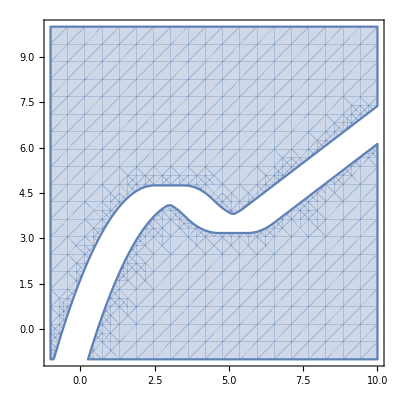

```mathematica
RegionPlot[numericdelaycond,  {xo, -1, 10}, {yo, -1, 10}]
```

```mathematica
dubinstraj = Piecewise[{{Sqrt[R^2-x^2],x>R/Sqrt[Tan[theta]^2+1]},{R*Sin[theta]-(-R*Cos[theta]+x)/Tan[theta],p<x},{R/Sin[theta]-p/Tan[theta]-Sqrt[p^2/Cos[theta]^2-(-2*p+x)^2]+Abs[p*Tan[theta]],b<x},{R/Sin[theta]-p/Tan[theta]+(-b+x)*(-2*p+x)*Abs(Cos[theta])/Sqrt[p^2-(b-2*p)^2*Cos[theta]^2]-Sqrt[-b^2*Cos[theta]^2+4*b*p*Cos[theta]^2-4*p^2*Cos[theta]^2+p^2]/Abs(Cos[theta])+Abs[p*Tan[theta]],True}}]
```

Piecewise[{{√(R^2-x^2), x>R/(√(1+Tan[theta]^2))}, {-((x-R Cos[theta]) Cot[theta])+R Sin[theta], p<x}, {Abs[p Tan[theta]]-p Cot[theta]+R Csc[theta]-√(-(-2 p+x)^2+p^2 Sec[theta]^2), b<x}, {Abs[p Tan[theta]]+(Abs (-b+x) (-2 p+x) Cos[theta])/(√(p^2-(b-2 p)^2 Cos[theta]^2))-(Cos[theta] √(p^2-b^2 Cos[theta]^2+4 b p Cos[theta]^2-4 p^2 Cos[theta]^2))/Abs-p Cot[theta]+R Csc[theta], True}}]

```mathematica
Timing[dubinscond = Resolve[ForAll[x, !RegionMember[RegularPolygon[{x, dubinstraj}, w, 6], {xo, yo}]], Reals]]
```

$Aborted

```mathematica
Timing[dubinscond = Resolve[ForAll[x, !RegionMember[Rectangle[{x-w, dubinstraj-h}, {x+w, dubinstraj+h}], {xo, yo}]], Reals]]
```

$Aborted

```mathematica
Timing[dubinscond = Resolve[ForAll[x, !RegionMember[Rectangle[{x-0.5, dubinstraj/.R-> 10/.theta-> pi/3/.p-> 3/.b->1-0.25}, {x+0.5, dubinstraj/.R-> 10/.theta-> pi/3/.p-> 3/.b->1+0.25}], {xo, yo}]], Reals]]
```

$Aborted

```mathematica
dubinstraj/.R-> 10/.theta-> pi/3/.p-> 3/.b->1
```

Piecewise[{{√(100-x^2), x>10/(√(1+Tan[pi/3]^2))}, {-((x-10 Cos[pi/3]) Cot[pi/3])+10 Sin[pi/3], 3<x}, {3 Abs[Tan[pi/3]]-3 Cot[pi/3]+10 Csc[pi/3]-√(-(-6+x)^2+9 Sec[pi/3]^2), 1<x}, {3 Abs[Tan[pi/3]]+(Abs (-6+x) (-1+x) Cos[pi/3])/(√(9-25 Cos[pi/3]^2))-(Cos[pi/3] √(9-25 Cos[pi/3]^2))/Abs-3 Cot[pi/3]+10 Csc[pi/3], True}}]

```mathematica
Manipulate[Plot[%20,{x,-8,8}],{pi,-8,8}]
```

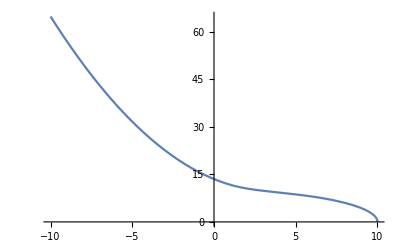

```mathematica
Plot[Piecewise[{{Sqrt[100-x^2],x>5},{-Sqrt[3]*(x-5)/3+5*Sqrt[3],x>3},{-Sqrt[36-(x-6)^2]+26*Sqrt[3]/3,x>1},{Sqrt[11]*(x-6)*(x-1)/11-Sqrt[11]+26*Sqrt[3]/3,True}}], {x, -10, 10}]
```